```mathematica
θh[x_]:=2π x/L;
θsk[r_]:=Piecewise[{{π,r<(R b-(R a)/2)},{0,r>(R b+(R a)/2)}},π(1-(r-(R b-(R a)/2))/((R b+(R a)/2)-(R b-(R a)/2)))](*/.a->R/5*);
m=(1-(T/Tc)^(3/2));
mh=m mz{Sin[θh[x]],0,Cos[θh[x]]};
msk=m mz{Sin[θsk[r]]  Cos[ϕ],Sin[θsk[r]]  Sin[ϕ],Cos[θsk[r]]};
mu=m{mx,my,mz}
H={0,0,Hz};
xh={1,0,0};
yh={0,1,0};
zh={0,0,1};
v={xh,yh,zh};
Msk=Table[TransformedField[ "Polar"->"Cartesian",msk.v⟦i⟧, {r,ϕ}->{x,y}],{i,1,3}]//Simplify
Mh=mh
Mu=mu
```

{mx (1-(T/Tc)^(3/2)),my (1-(T/Tc)^(3/2)),mz (1-(T/Tc)^(3/2))}

{Piecewise[{{0, a R+2 √(x^2+y^2)<2 b R||2 √(x^2+y^2)>(a+2 b) R}, {-(mz (-1+(T/Tc)^(3/2)) x Cos[(π (-b R+√(x^2+y^2)))/(a R)])/(√(x^2+y^2)), True}}],Piecewise[{{0, a R+2 √(x^2+y^2)<2 b R||2 √(x^2+y^2)>(a+2 b) R}, {-(mz (-1+(T/Tc)^(3/2)) y Cos[(π (-b R+√(x^2+y^2)))/(a R)])/(√(x^2+y^2)), True}}],-mz (-1+(T/Tc)^(3/2)) Cos[Piecewise[{{π, a R+2 √(x^2+y^2)<2 b R}, {0, 2 √(x^2+y^2)>(a+2 b) R}, {(π (a R+2 b R-2 √(x^2+y^2)))/(2 a R), True}}]]}

{mz (1-(T/Tc)^(3/2)) Sin[(2 π x)/L],0,mz (1-(T/Tc)^(3/2)) Cos[(2 π x)/L]}

{mx (1-(T/Tc)^(3/2)),my (1-(T/Tc)^(3/2)),mz (1-(T/Tc)^(3/2))}

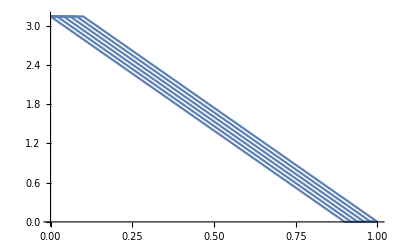

```mathematica
Plot[Table[θsk[r]/.{R->1,a->0.9},{b,0.45,0.55,0.02}],{r,0,1}]
```

```mathematica
rvec={x,y,z}
fDM[M_]:=Sum[d m^n Cross[zh,v⟦i⟧].Cross[M,D[M,rvec⟦i⟧]],{i,1,2}]
```

{x,y,z}

```mathematica
fsk=Simplify[TransformedField["Cartesian"-> "Polar",Aex Div[Msk,{x,y,z}]^2-μ0 Msk.H M0+kd(Msk.zh)^2-ku(Msk.zh)^2+fDM[Msk],{x,y}->{r,ϕ}],{r>0,ϕ∈Reals,b<=(1-a/2),b>=a/2,a>=0,a<=1}]//FullSimplify
fh=Aex Div[Mh,{x,y,z}]^2-μ0 Mh.H M0+kd(Mh.zh)^2-ku(Mh.zh)^2+fDM[Mh]//FullSimplify
fu=Aex Div[Mu,{x,y,z}]^2-μ0 Mu.H M0+kd(Mu.zh)^2-ku(Mu.zh)^2+fDM[Mu]//FullSimplify
```

Piecewise[{{mz (-2 kd mz (T/Tc)^(3/2)+2 ku mz (T/Tc)^(3/2)+((kd-ku) mz (T^3+Tc^3))/Tc^3-Hz M0 μ0+Hz M0 (T/Tc)^(3/2) μ0), 2 r+a R≥2 b R&&(a+2 b) R<2 r}, {mz (-2 kd mz (T/Tc)^(3/2)+2 ku mz (T/Tc)^(3/2)+((kd-ku) mz (T^3+Tc^3))/Tc^3+Hz M0 μ0-Hz M0 (T/Tc)^(3/2) μ0), 2 r+a R<2 b R}, {1/(2 a^2 r^2 R^2 Tc^3)mz (-mz (Aex π^2 r^2-a^2 (Aex+(-kd+ku) r^2) R^2) (T^3+Tc^3-2 (T/Tc)^(3/2) Tc^3) Cos[(2 π (-r+b R))/(a R)]+2 a^2 Hz M0 r^2 R^2 Tc^2 (-T √(T/Tc)+Tc) μ0 Sin[(π (-r+b R))/(a R)]+mz (T^3+Tc^3-2 (T/Tc)^(3/2) Tc^3) (Aex (π^2 r^2+a^2 R^2)+a r^2 R (a (kd-ku) R-2 d π (1-(T/Tc)^(3/2))^n)+a r R (2 Aex π-a d R (1-(T/Tc)^(3/2))^n) Sin[(2 π (-r+b R))/(a R)])), True}}]

(mz (2 Hz M0 (T √(T/Tc)-Tc) Tc^2 μ0 Cos[(2 π x)/L]+(mz (T^3+Tc^3-2 (T/Tc)^(3/2) Tc^3) (4 d L π (1-(T/Tc)^(3/2))^n+((kd-ku) L^2+4 Aex π^2) (1+Cos[(4 π x)/L])))/L^2))/(2 Tc^3)

(mz (T √(T/Tc)-Tc) (kd mz (T √(T/Tc)-Tc)+ku mz (-T √(T/Tc)+Tc)+Hz M0 Tc μ0))/Tc^2

```mathematica
Fsk=Assuming[R∈PositiveReals&&b<(1-a/2)&&b>a/2&&a<1&&a>0,1/(π R^2)∫_0^(2π) (∫_0^R fsk rⅆr)ⅆϕ]
Fh=1/L∫_0^L fh ⅆx//FullSimplify
Fu=1/L∫_0^L fu ⅆx//FullSimplify
```

1/(2 a π^2 R^2 Tc^3)(2 Aex b mz^2 π^4 T^3+2 a kd mz^2 π^2 R^2 T^3-2 a^2 b kd mz^2 π^2 R^2 T^3-2 a ku mz^2 π^2 R^2 T^3+2 a^2 b ku mz^2 π^2 R^2 T^3-4 a b d mz^2 π^3 R T^3 (1-(T/Tc)^(3/2))^n-4 Aex b mz^2 π^4 T √(T/Tc) Tc^2-4 a kd mz^2 π^2 R^2 T √(T/Tc) Tc^2+4 a^2 b kd mz^2 π^2 R^2 T √(T/Tc) Tc^2+4 a ku mz^2 π^2 R^2 T √(T/Tc) Tc^2-4 a^2 b ku mz^2 π^2 R^2 T √(T/Tc) Tc^2+8 a b d mz^2 π^3 R T (1-(T/Tc)^(3/2))^n √(T/Tc) Tc^2+2 Aex b mz^2 π^4 Tc^3+2 a kd mz^2 π^2 R^2 Tc^3-2 a^2 b kd mz^2 π^2 R^2 Tc^3-2 a ku mz^2 π^2 R^2 Tc^3+2 a^2 b ku mz^2 π^2 R^2 Tc^3-4 a b d mz^2 π^3 R (1-(T/Tc)^(3/2))^n Tc^3+8 a^3 Hz M0 mz R^2 T √(T/Tc) Tc^2 μ0+2 a Hz M0 mz π^2 R^2 T √(T/Tc) Tc^2 μ0-a^3 Hz M0 mz π^2 R^2 T √(T/Tc) Tc^2 μ0-4 a b^2 Hz M0 mz π^2 R^2 T √(T/Tc) Tc^2 μ0-8 a^3 Hz M0 mz R^2 Tc^3 μ0-2 a Hz M0 mz π^2 R^2 Tc^3 μ0+a^3 Hz M0 mz π^2 R^2 Tc^3 μ0+4 a b^2 Hz M0 mz π^2 R^2 Tc^3 μ0+2 a Aex mz^2 π^2 T^3 Cos[(2 b π)/a] CosIntegral[-((a+2 b) π)/a]-4 a Aex mz^2 π^2 T √(T/Tc) Tc^2 Cos[(2 b π)/a] CosIntegral[-((a+2 b) π)/a]+2 a Aex mz^2 π^2 Tc^3 Cos[(2 b π)/a] CosIntegral[-((a+2 b) π)/a]-2 a Aex mz^2 π^2 T^3 Cos[(2 b π)/a] CosIntegral[π-(2 b π)/a]+4 a Aex mz^2 π^2 T √(T/Tc) Tc^2 Cos[(2 b π)/a] CosIntegral[π-(2 b π)/a]-2 a Aex mz^2 π^2 Tc^3 Cos[(2 b π)/a] CosIntegral[π-(2 b π)/a]+2 a Aex mz^2 π^2 T^3 Log[-(a+2 b)/(a-2 b)]-4 a Aex mz^2 π^2 T √(T/Tc) Tc^2 Log[-(a+2 b)/(a-2 b)]+2 a Aex mz^2 π^2 Tc^3 Log[-(a+2 b)/(a-2 b)]+2 a Aex mz^2 π^2 T^3 Sin[(2 b π)/a] SinIntegral[π-(2 b π)/a]-4 a Aex mz^2 π^2 T √(T/Tc) Tc^2 Sin[(2 b π)/a] SinIntegral[π-(2 b π)/a]+2 a Aex mz^2 π^2 Tc^3 Sin[(2 b π)/a] SinIntegral[π-(2 b π)/a]+2 a Aex mz^2 π^2 T^3 Sin[(2 b π)/a] SinIntegral[π+(2 b π)/a]-4 a Aex mz^2 π^2 T √(T/Tc) Tc^2 Sin[(2 b π)/a] SinIntegral[π+(2 b π)/a]+2 a Aex mz^2 π^2 Tc^3 Sin[(2 b π)/a] SinIntegral[π+(2 b π)/a])

(mz^2 (4 Aex π^2+L (kd L-ku L+4 d π (1-(T/Tc)^(3/2))^n)) (T^3+Tc^3-2 (T/Tc)^(3/2) Tc^3))/(2 L^2 Tc^3)

(mz (T √(T/Tc)-Tc) (kd mz (T √(T/Tc)-Tc)+ku mz (-T √(T/Tc)+Tc)+Hz M0 Tc μ0))/Tc^2

```mathematica
Fesk=Collect[Fsk,{SinIntegral[_],CosIntegral[_],(1-(T/Tc)^(3/2))},FullSimplify]
Feh=FullSimplify[Fh,L>0]
Feu=Fu
```

(Aex mz^2 (T^3+Tc^3-2 (T/Tc)^(3/2) Tc^3) Cos[(2 b π)/a] CosIntegral[-((a+2 b) π)/a])/(R^2 Tc^3)-(Aex mz^2 (T^3+Tc^3-2 (T/Tc)^(3/2) Tc^3) Cos[(2 b π)/a] CosIntegral[π-(2 b π)/a])/(R^2 Tc^3)+1/(2 a π^2 R^2 Tc^3)mz (2 Aex b mz π^4 (T^3+Tc^3-2 (T/Tc)^(3/2) Tc^3)+a R (8 b d mz π^3 (1-(T/Tc)^(3/2))^n (T/Tc)^(3/2) Tc^3-4 b d mz π^3 (1-(T/Tc)^(3/2))^n (T^3+Tc^3)-2 (-1+a b) kd mz π^2 R (T^3+Tc^3-2 (T/Tc)^(3/2) Tc^3)+2 (-1+a b) ku mz π^2 R (T^3+Tc^3-2 (T/Tc)^(3/2) Tc^3)+Hz M0 (-8 a^2+(-2+a^2+4 b^2) π^2) R Tc^3 μ0+8 a^2 Hz M0 R (T/Tc)^(3/2) Tc^3 μ0+2 Hz M0 π^2 R (T/Tc)^(3/2) Tc^3 μ0-a^2 Hz M0 π^2 R (T/Tc)^(3/2) Tc^3 μ0-4 b^2 Hz M0 π^2 R (T/Tc)^(3/2) Tc^3 μ0)+2 a Aex mz π^2 (T^3+Tc^3-2 (T/Tc)^(3/2) Tc^3) Log[1-(2 a)/(a-2 b)])+(Aex mz^2 (T^3+Tc^3-2 (T/Tc)^(3/2) Tc^3) Sin[(2 b π)/a] SinIntegral[π-(2 b π)/a])/(R^2 Tc^3)+(Aex mz^2 (T^3+Tc^3-2 (T/Tc)^(3/2) Tc^3) Sin[(2 b π)/a] SinIntegral[π+(2 b π)/a])/(R^2 Tc^3)

(mz^2 (4 Aex π^2+L (kd L-ku L+4 d π (1-(T/Tc)^(3/2))^n)) (T^3+Tc^3-2 (T/Tc)^(3/2) Tc^3))/(2 L^2 Tc^3)

(mz (T √(T/Tc)-Tc) (kd mz (T √(T/Tc)-Tc)+ku mz (-T √(T/Tc)+Tc)+Hz M0 Tc μ0))/Tc^2

```mathematica
Fesk=Fesk//Simplify
```

1/(2 R^2 Tc^3)mz (8 b d mz π R (1-(T/Tc)^(3/2))^n (T/Tc)^(3/2) Tc^3-4 b d mz π R (1-(T/Tc)^(3/2))^n (T^3+Tc^3)+(2 Aex b mz π^2 (T^3+Tc^3-2 (T/Tc)^(3/2) Tc^3))/a-2 (-1+a b) kd mz R^2 (T^3+Tc^3-2 (T/Tc)^(3/2) Tc^3)+2 (-1+a b) ku mz R^2 (T^3+Tc^3-2 (T/Tc)^(3/2) Tc^3)+(Hz M0 (-8 a^2+(-2+a^2+4 b^2) π^2) R^2 Tc^3 μ0)/π^2+2 Hz M0 R^2 (T/Tc)^(3/2) Tc^3 μ0-a^2 Hz M0 R^2 (T/Tc)^(3/2) Tc^3 μ0-4 b^2 Hz M0 R^2 (T/Tc)^(3/2) Tc^3 μ0+(8 a^2 Hz M0 R^2 (T/Tc)^(3/2) Tc^3 μ0)/π^2+2 Aex mz (T^3+Tc^3-2 (T/Tc)^(3/2) Tc^3) Cos[(2 b π)/a] CosIntegral[-((a+2 b) π)/a]-2 Aex mz (T^3+Tc^3-2 (T/Tc)^(3/2) Tc^3) Cos[(2 b π)/a] CosIntegral[π-(2 b π)/a]+2 Aex mz (T^3+Tc^3-2 (T/Tc)^(3/2) Tc^3) Log[1-(2 a)/(a-2 b)]+2 Aex mz (T^3+Tc^3-2 (T/Tc)^(3/2) Tc^3) Sin[(2 b π)/a] SinIntegral[π-(2 b π)/a]+2 Aex mz (T^3+Tc^3-2 (T/Tc)^(3/2) Tc^3) Sin[(2 b π)/a] SinIntegral[π+(2 b π)/a])

```mathematica
Solutionsk=Solve[D[Fesk,R]==0,R]//FullSimplify
Solutionh=Solve[D[Feh,L]==0,L]//FullSimplify
```

{{R→1/(a b d π)Aex (1-(T/Tc)^(3/2))^-n (b π^2+a (Cos[(2 b π)/a] (CosIntegral[-((a+2 b) π)/a]-CosIntegral[π-(2 b π)/a])+Log[1-(2 a)/(a-2 b)]+Sin[(2 b π)/a] (SinIntegral[π-(2 b π)/a]+SinIntegral[π+(2 b π)/a])))}}

{{L→-(2 Aex π (1-(T/Tc)^(3/2))^-n)/d}}

```mathematica
Xf[a_,b_]:=(b π^2+a (Cos[(2 b π)/a] (CosIntegral[-((a+2 b) π)/a]-CosIntegral[π-(2 b π)/a])+Log[1-(2 a)/(a-2 b)]+Sin[(2 b π)/a] (SinIntegral[π-(2 b π)/a]+SinIntegral[π+(2 b π)/a])))
```

```mathematica
Limit[Xf[a,b],{a->1,b-> 1/2}]
```

EulerGamma+π^2/2-CosIntegral[2 π]+Log[2 π]

```mathematica
Fmsk=Collect[Fesk/.Solutionsk⟦1,1⟧//.Xf[a,b]-> X,{(1-(T/Tc)^(3/2)),d^2/Aex,X},FullSimplify]//.Xf[a,b]-> X
```

-(a b^2 d^2 mz^2 π^2 (1-(T/Tc)^(3/2))^(2 n) (T^3+Tc^3-2 (T/Tc)^(3/2) Tc^3))/(Aex Tc^3 X)-(mz (2 (-1+a b) kd mz π^2 (T^3+Tc^3-2 (T/Tc)^(3/2) Tc^3)-2 (-1+a b) ku mz π^2 (T^3+Tc^3-2 (T/Tc)^(3/2) Tc^3)+Hz M0 (-8 a^2+(-2+a^2+4 b^2) π^2) (T √(T/Tc)-Tc) Tc^2 μ0))/(2 π^2 Tc^3)

```mathematica
Fmh=Feh/.Solutionh⟦1,1⟧//Simplify
```

(mz^2 (Aex (kd-ku)-d^2 (1-(T/Tc)^(3/2))^(2 n)) (T^3+Tc^3-2 (T/Tc)^(3/2) Tc^3))/(2 Aex Tc^3)

```mathematica
Fmu=Feu
```

(mz (T √(T/Tc)-Tc) (kd mz (T √(T/Tc)-Tc)+ku mz (-T √(T/Tc)+Tc)+Hz M0 Tc μ0))/Tc^2

```mathematica
ρ0sk=Collect[Fmsk/.Solutionsk⟦1,1⟧/.T->0,{d^2/Aex},FullSimplify]/.a->1/.b->0.5
ρ0h=Fmh/.Solutionh⟦1,1⟧/.T->0//FullSimplify
ρ0u=Fmu/.T->0
```

-(2.4674 d^2 mz^2)/(Aex X)+1/2 mz (1. kd mz-1. ku mz-0.810569 Hz M0 μ0)

-((d^2+Aex (-kd+ku)) mz^2)/(2 Aex)

-(mz (-kd mz Tc+ku mz Tc+Hz M0 Tc μ0))/Tc

```mathematica
EulerGamma//N
```

0.577216

```mathematica
CosIntegral[2π]//N
```

-0.0225607

```mathematica
ρ0sk//N//Expand
```

0.5 kd mz^2-0.5 ku mz^2-(2.4674 d^2 mz^2)/(Aex X)-0.405285 Hz M0 mz μ0

```mathematica
ACir=3/4 π a^2;
AHex=(3 √3)/2 a^2;
ratio=ACir/AHex
```

π/(2 √3)

```mathematica
FE=ratio Fmsk + (1-ratio) Fmu//Simplify
```

-1/(12 Aex π Tc^3 X)mz (2 √3 a b mz π^2 (T^3+Tc^3-2 (T/Tc)^(3/2) Tc^3) (b d^2 π^2 (1-(T/Tc)^(3/2))^(2 n)+Aex (kd-ku) X)+√3 a^2 Aex Hz M0 (-8+π^2) (T √(T/Tc)-Tc) Tc^2 X μ0+4 Aex π X (-3 kd mz (T^3+Tc^3-2 (T/Tc)^(3/2) Tc^3)+3 ku mz (T^3+Tc^3-2 (T/Tc)^(3/2) Tc^3)+Hz M0 (-3+√3 b^2 π) (T √(T/Tc)-Tc) Tc^2 μ0))

```mathematica
SetDirectory[NotebookDirectory[]]
Get["state-Aug25.mx"]
```

/home/sid/Academics/Case Western Reserve University/Projects/GL-Skyrmion/Workspace

```mathematica
ℏ=(6.63 10^-34)/(2π);kb=1.38 10^-23;
Parameters={d->(*10^3 √(6.5 10^-12)*) 3 2 10^-3,Tc->270,M0-> 362 10^3,kd-> 2.62 10^5,ku->0.2 1.58 10^6(*419303+2.62 10^5*),μ0-> 0.1,Aex->(* 6.5 10^-12*)10 6.5 10^-12,n->2}//N
```

{d→0.006,Tc→270.,M0→362000.,kd→262000.,ku→316000.,μ0→0.1,Aex→6.5×10^-11,n→2.}

```mathematica
Table[Equal@@Parameters⟦i⟧,{i,1,Length[Parameters]}]
```

{d==0.006,Tc==270.,M0==362000.,kd==262000.,ku==316000.,μ0==0.1,Aex==6.5×10^-11,n==2.}

```mathematica
aval=0.9;bval=0.55;Xval=Limit[Xf[a,b],{a->aval,b->bval}]
(*ContourPlot[Ordering[{FE ,Fmh,Fmu}/.X->Xval/.a->aval/.b->bval/.mz->1/.Parameters,1],{T,0,120},{Hz,0,15},Axes->True,Frame->False,ColorFunction->(If[#1≠ 0 ,Green,Blue]&),AxesLabel->{"T (K)","H (kOe)"},ImageSize->Large]*)
opac=0.2;
A=Table[{bvalue,Xvalue=Chop[Limit[Xf[a,b]/.a-> aval,b->bvalue]],RegionPlot[{ (Fmh<FE && Fmh<Fmu) /.X-> Xvalue/.a->aval/.b->bvalue/.Parameters/.mz->Sign[Hz],(FE<Fmh && FE<Fmu)/.X-> Xvalue/.a->aval/.b->bvalue/.Parameters/.mz->Sign[Hz], (Fmu<FE && Fmu<Fmh)/.X-> Xvalue/.a->aval/.b->bvalue/.Parameters/.mz->Sign[Hz]},{T,0,120},{Hz,0,15},Axes->True,Frame->False,MaxRecursion->10,BoundaryStyle-> None,AxesLabel->{"T (K)","H (kOe)"},ImageSize->Large,LabelStyle->Large, PlotStyle->{Opacity[opac,Orange],Opacity[opac,Blue],Opacity[opac,Green]}]},{bvalue,1-aval/2,aval/2,-0.02}]//Parallelize
```

7.06963+0. ⅈ

{{0.55,7.06963,-Graphics-},{0.53,6.95311,-Graphics-},{0.51,6.84705,-Graphics-},{0.49,6.75443,-Graphics-},{0.47,6.68016,-Graphics-},{0.45,6.63521,-Graphics-}}

```mathematica
aval=0.9;bval=0.55;opac=0.0;
Xvalue=Chop[Limit[Xf[a,b]/.a-> aval,b->bval]]
A2=RegionPlot[{ (Fmh<FE && Fmh<Fmu) /.X-> Xvalue/.a->aval/.b->bval/.Parameters/.mz->Sign[Hz],(FE<Fmh && FE<Fmu)/.X-> Xvalue/.a->aval/.b->bval/.Parameters/.mz->Sign[Hz], (Fmu<FE && Fmu<Fmh)/.X-> Xvalue/.a->aval/.b->bval/.Parameters/.mz->Sign[Hz]},{T,0,120},{Hz,0,15},Axes->True,Frame->False,MaxRecursion->10,BoundaryStyle-> None,AxesLabel->{"T (K)","H (kOe)"},ImageSize->Large,PlotLabels->Placed[{"Helix","SkX","Uniform FM"},Center],LabelStyle->Large, PlotStyle->{Opacity[opac,Yellow],Opacity[opac,Blue],Opacity[opac,Green]}]
```

7.06963

-Graphics-

```mathematica
Xvalue=Chop[Limit[Xf[a,b]/.a-> aval,b->0.55]]
B=DensityPlot[If[Ordering[{ Fmh,FE,Fmu}/.X-> Xvalue/.a->aval/.b->0.55/.mz->Sign[Hz]/.Parameters,1]⟦1⟧==2,Chop[10^-12(ratio π R^2)^-1/.Solutionsk/.X-> Xvalue/.a->aval/.b->0.55/.mz->1/.Parameters]⟦1⟧Sign[Hz],0],{T,0,120},{Hz,15,-15},Axes->True,Frame-> False,PlotLegends-> Placed[BarLegend[Automatic,LegendMarkerSize->150,LegendLabel->"Skyrmion Density (μm^-2)"],{After,Top}],AxesOrigin->{0,15}, PlotPoints->300,AxesLabel->{"T (K)","H (kOe)"},ImageSize->Large,ColorFunction->(Blend[{Blue,Cyan,Green,Yellow,Red},#]&),LabelStyle->Large, ScalingFunctions->{Identity,"Reverse",Identity}]
```

7.06963

-Graphics-

```mathematica
Export["Density-vs-H-T.jpg",B]
```

Density-vs-H-T.jpg

```mathematica
Export["Final.jpg",Overlay[Append[Table[A⟦i,3⟧,{i,1,Length[A]}],A2]]]
```

Final.jpg

```mathematica
Export["Final2.jpg",Overlay[Table[A⟦i,3⟧,{i,1,Length[A]}]]]
```

Final2.jpg

```mathematica
Plot[θsk[r]/.b->0.6 /.a->0.8/.R-> 1,{r,0,1},PlotRange->All]
```

-Graphics-

```mathematica
rules=Flatten[{X-> Xval,a->aval,b->bval,mz->1,Parameters,T->t}]
Table[Plot[{FE/.rules,Fmh/.rules,Fmu/.rules},{Hz,0,20}],{t,0,100,20}]
```

{X→7.3948+0. ⅈ,a→0.9,b→0.6,mz→1,d→0.006,Tc→270.,M0→362000.,kd→262000.,ku→316000.,μ0→0.1,Aex→6.5×10^-11,n→2.,T→t}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
μ0 M0 20 0.4/.Parameters
```

289600.

```mathematica
{d^2/Aex,ku-kd}/.Parameters
```

{553846.,54000.}

```mathematica
Hzz=Solve[FE==ρ0h/.mz->Min[1,Hz/(2Aex)]/.Parameters/.T->0,Hz,PositiveReals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Hz→ConditionalExpression[(8.91038×10^37 a b^2-4.49215×10^36 X-8.8024×10^35 a b X)/(-6.50663×10^35 X+5.58902×10^34 a^2 X+1.18017×10^36 b^2 X), ]}}

```mathematica
Hz1=Normal[Assuming[a<1&&a>0&&d>0&&Tc>0&&M0>0&&kd>0&&ku>kd&&μ0>0&&Aex>0&&n>0&&X>0&&b<(1-a/2)&&b>a/2,Solve[FE==Fmh/.mz->1/.T->0/.X[a]->X//Expand,Hz,PositiveReals]]]//FullSimplify
```

{{Hz→(2 π (-3 (d^2+Aex (kd-ku)) X+√3 a b π (b d^2 π^2+Aex (kd-ku) X)))/(Aex M0 (-12 π+√3 (4 b^2 π^2+a^2 (-8+π^2))) X μ0)}}

```mathematica
Hz2=Normal[Assuming[a<1&&a>0&&d>0&&Tc>0&&M0>0&&kd>0&&ku>kd&&μ0>0&&Aex>0&&n>0&&X>0&&b<(1-a/2)&&b>a/2,Solve[FE==Fmu/.mz->1/.T->0/.X[a]->X,Hz,PositiveReals]]]//FullSimplify
```

{{Hz→(2 a b π^2 (b d^2 π^2+Aex (kd-ku) X))/(Aex M0 (4 b^2 π^2+a^2 (-8+π^2)) X μ0)}}

```mathematica
ParameterSolutions=Solve[{Equal@@Hz1⟦1,1⟧/.Hz-> Hzc1/.ku-> kd+χ/.Aex->J0 ,Equal@@Hz2⟦1,1⟧/.Hz->Hzc2 /.ku-> kd+χ/.Aex->J0},{χ,J0}]//FullSimplify
```

{{χ→(M0 (4 a b^2 π^4 (-3 Hzc1+√3 b^2 (Hzc1-Hzc2) π)+√3 a^3 b^2 (Hzc1-Hzc2) π^3 (-8+π^2)+12 b^2 Hzc2 π^2 X+3 a^2 Hzc2 (-8+π^2) X) μ0)/(6 a b π^2 (b π^2-X)),J0→(6 a b d^2 π^2 (-b π^2+X))/(M0 (24 a^2 Hzc2+8 √3 a^3 b (Hzc1-Hzc2) π-3 (-4 a b Hzc1+a^2 Hzc2+4 b^2 Hzc2) π^2+√3 b (a^3+4 a b^2) (-Hzc1+Hzc2) π^3) X μ0)}}

```mathematica
ParameterSolutions/.Parameters//N
```

{{χ→(611.304 (389.636 a b^2 (-3. Hzc1+5.4414 b^2 (Hzc1-1. Hzc2))+100.406 a^3 b^2 (Hzc1-1. Hzc2)+5.60881 a^2 Hzc2 X+118.435 b^2 Hzc2 X))/(a b (9.8696 b-1. X)),J0→(5.88905×10^-8 a b (-9.8696 b+X))/((43.5312 a^3 b (Hzc1-1. Hzc2)+24. a^2 Hzc2+53.7044 b (a^3+4. a b^2) (-1. Hzc1+Hzc2)-29.6088 (-4. a b Hzc1+a^2 Hzc2+4. b^2 Hzc2)) X)}}

```mathematica
ParameterSolutions/.Parameters/.Hzc1->10/.Hzc2->5
```

{{χ→(611.304 (4 a b^2 π^4 (-30+5 √3 b^2 π)+5 √3 a^3 b^2 π^3 (-8+π^2)+60 b^2 π^2 X+15 a^2 (-8+π^2) X))/(a b (b π^2-X)),J0→(5.88905×10^-8 a b (-b π^2+X))/((120 a^2+40 √3 a^3 b π-3 (5 a^2-40 a b+20 b^2) π^2-5 √3 b (a^3+4 a b^2) π^3) X)}}

```mathematica
Plot[{FE/.mz->Min[1,Hz/(2Aex)]/.Parameters/.T->0,Fmh/.mz->Min[1,Hz/(2Aex)]/.Parameters/.T->0,Fmu/.mz->Min[1,Hz/(2Aex)]/.Parameters/.T->0},{ratio,0,1}]
```

-Graphics-

```mathematica
SolD=Normal[Solve[Equal@@Hz2⟦1,1⟧/.Hz-> Hzc2/.ku-> kd+χ/.Aex->J0/.d-> D0,D0,PositiveReals]//FullSimplify]
```

{{D0→(√(J0 X ((4 Hzc2 M0 π^2 μ0)/a+(a Hzc2 M0 (-8+π^2) μ0)/b^2+(2 π^2 χ)/b)))/(√2 π^2)}}

```mathematica
SolD/.ParameterSolutions⟦1⟧/.Parameters/.Hzc1->10/.Hzc2->5
```

{{D0→0.0000173863 √((a b (-b π^2+X) ((7.14559×10^6)/a+(338398. a)/b^2+(12066.7 (4 a b^2 π^4 (-30+5 √3 b^2 π)+5 √3 a^3 b^2 π^3 (-8+π^2)+60 b^2 π^2 X+15 a^2 (-8+π^2) X))/(a b^2 (b π^2-X))))/(120 a^2+40 √3 a^3 b π-3 (5 a^2-40 a b+20 b^2) π^2-5 √3 b (a^3+4 a b^2) π^3))}}

```mathematica
msk⟦3⟧
```

mz (1-(T/Tc)^(3/2)) Cos[Piecewise[{{π, r<-(a R)/2+b R}, {0, r>(a R)/2+b R}, {π (1-(r+(a R)/2-b R)/(a R)), True}}]]

```mathematica
MeanMagz=Assuming[R∈PositiveReals&&a<1&&a>0&&d>0&&Tc>0&&M0>0&&kd>0&&ku>kd&&μ0>0&&Aex>0&&n>0&&X>0&&b<(1-a/2)&&b>a/2,∫_0^(2π) ∫_0^R (msk⟦3⟧/.T-> 0)rⅆrⅆϕ]/(π R^2)//FullSimplify
MeanMagz//N
```

mz (1-2 b^2+a^2 (-1/2+4/π^2))

(1.-0.0947153 a^2-2. b^2) mz

```mathematica
MeanMagy=Assuming[R∈PositiveReals&&a<1&&a>0&&d>0&&Tc>0&&M0>0&&kd>0&&ku>kd&&μ0>0&&Aex>0&&n>0&&X>0&&b<(1-a/2)&&b>a/2,∫_0^(2π) ∫_0^R (msk⟦2⟧/.T-> 0)rⅆrⅆϕ]/(π R^2)//FullSimplify
MeanMagy//N
```

0

0.

```mathematica
ContourPlot[Xf[a,b],{b,0,1},{a,0,1},PlotLegends->Automatic]
```

-Graphics-

```mathematica
DumpSave["state-Aug25.mx","Global`"]
```

{Global`}

```mathematica
π(1-(r-(R b-(R a)/2))/((R b+(R a)/2)-(R b-(R a)/2)))//FullSimplify
```

(π (-2 r+(a+2 b) R))/(2 a R)